```mathematica
Parametrization of GPDs used in GK model for pi0 production
```

```mathematica
\tilde{H}
```

NIntegrate::nlim: y = 1.11111 (-0.1+x) HeavisideTheta[-0.1+x] is not a valid limit of integration.

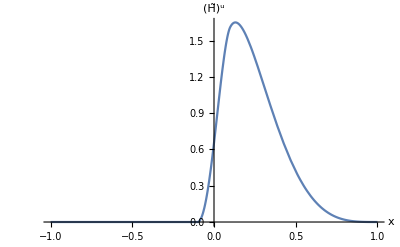

NIntegrate::nlim: y = 1.11111 (-0.1+x) HeavisideTheta[-0.1+x] is not a valid limit of integration.

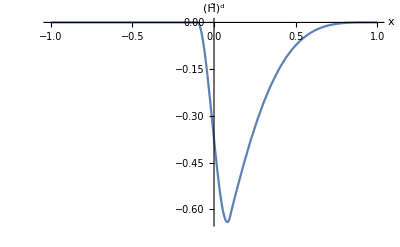

```mathematica
cu=List[cu=0.213,0.929,12.59,-12.57,0.0];
cd=List[cd=-0.204,-0.940,-0.314,1.524,0.0];
pu[y_]:=y^(-0.32)*(1-y)^0*(0.213+0.929*Sqrt[y]+12.59*y-12.57*y^(3/2)+0.0*y^2);
pd[y_]:=y^(-0.32)*(1-y)^0*(-0.204-0.940*Sqrt[y]-0.314*y+1.524*y^(3/2)+0.0*y^2);
fu[y_]:=(-0.961*Log[y]+0.545)*(1-y)^3+(1.264)*y*(1-y)^2;
fd[y_]:=(-0.861*Log[y]+0.206)*(1-y)^3+(4.198)*y*(1-y)^2;

lowery[x_,xi_]:=HeavisideTheta[x-xi]*(x-xi)/(1-xi);
uppery[x_,xi_]:=HeavisideTheta[x+xi]*(x+xi)/(1+xi);

Htildeu[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pu[y]*Exp[t*fu[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];
Htilded[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pd[y]*Exp[t*fd[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];

Plot[Htildeu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^u"}]

Plot[Htilded[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^d"}]
```

## \tilde{E}

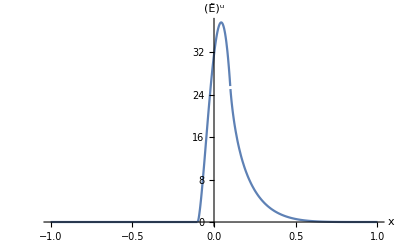

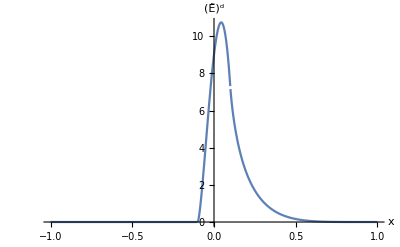

```mathematica
EtildeAlpha0=0.48;
EtildeAlphaprime=0.45;
Etildeb=0.9;
EtildeNu=14;
EtildeNd=4;

k[t_]=EtildeAlpha0+EtildeAlphaprime*t;

(*When x+xi < 0.0*)
D1=0.0;
(*When x-xi < 0.0*)
D2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-k[t])*(xi^2-x+(2+i-k[t])*xi*(1-x))/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]));
(*Else*)
D3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-k[t])-((x-xi)/(1-xi))^(2+i-k[t]))+xi*(1-x)*(2+i-k[t])*(((x+xi)/(1+xi))^(2+i-k[t])+((x-xi)/(1-xi))^(2+i-k[t])));

DD[i_,x_,xi_,t_]= If[x<-xi,D1,If[-xi≤x≤xi,D2[i,x,xi,t],D3[i,x,xi,t]]];

Etildeu[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNu*DD[0,x,xi,t]-2*EtildeNu*DD[1,x,xi,t]+EtildeNu*DD[2,x,xi,t]);
Etilded[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNd*DD[0,x,xi,t]-2*EtildeNd*DD[1,x,xi,t]+EtildeNd*DD[2,x,xi,t]);

Plot[Etildeu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^u"}]

Plot[Etilded[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^d"}]
```

## H_T and \bar{E}_T

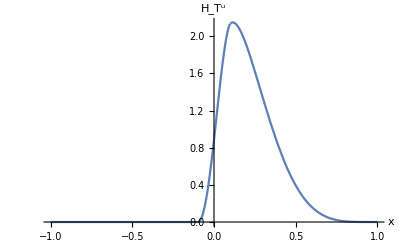

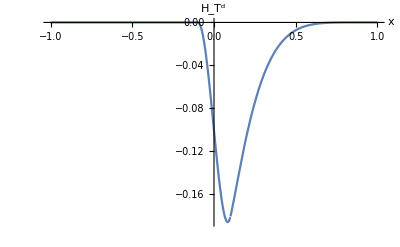

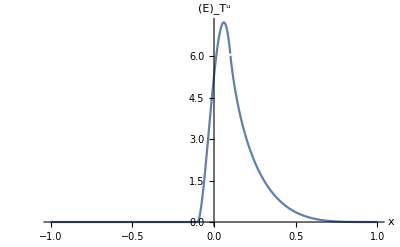

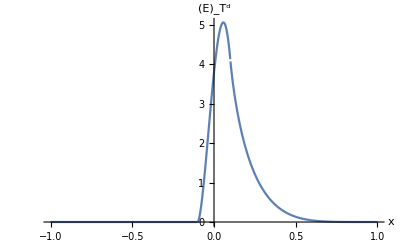

```mathematica
HTAlpha0=-0.17;
HTAlphaprime=0.45;
HTb=0.0;
HTNu=1.1;
HTNd=-0.3;

EbarTAlpha0=0.3;
EbarTAlphaprime=0.45;
EbarTb=0.5;
EbarTNu=4.83;
EbarTNd=3.57;

HTk[t_]=HTAlpha0+HTAlphaprime*t;
EbarTk[t_]=EbarTAlpha0+EbarTAlphaprime*t;

(*When x+xi < 0.0*)
HTD1=0.0;
(*When x-xi < 0.0*)
HTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-HTk[t])*(xi^2-x+(2+i-HTk[t])*xi*(1-x))/((1+i-HTk[t])*(2+i-HTk[t])*(3+i-HTk[t]));
(*Else*)
HTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-HTk[t])*(2+i-HTk[t])*(3+i-HTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-HTk[t])-((x-xi)/(1-xi))^(2+i-HTk[t]))+xi*(1-x)*(2+i-HTk[t])*(((x+xi)/(1+xi))^(2+i-HTk[t])+((x-xi)/(1-xi))^(2+i-HTk[t])));

HTDD[i_,x_,xi_,t_]= If[x<-xi,HTD1,If[-xi≤x≤xi,HTD2[i,x,xi,t],HTD3[i,x,xi,t]]];

(*When x+xi < 0.0*)
EbarTD1=0.0;
(*When x-xi < 0.0*)
EbarTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-EbarTk[t])*(xi^2-x+(2+i-EbarTk[t])*xi*(1-x))/((1+i-EbarTk[t])*(2+i-EbarTk[t])*(3+i-EbarTk[t]));
(*Else*)
EbarTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-EbarTk[t])*(2+i-EbarTk[t])*(3+i-EbarTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-EbarTk[t])-((x-xi)/(1-xi))^(2+i-EbarTk[t]))+xi*(1-x)*(2+i-EbarTk[t])*(((x+xi)/(1+xi))^(2+i-EbarTk[t])+((x-xi)/(1-xi))^(2+i-EbarTk[t])));

EbarTDD[i_,x_,xi_,t_]= If[x<-xi,EbarTD1,If[-xi≤x≤xi,EbarTD2[i,x,xi,t],EbarTD3[i,x,xi,t]]];

HTu[x_,xi_,t_]:=HTNu*Exp[HTb*t]*(3.653*HTDD[0,x,xi,t]-0.583*HTDD[0.5,x,xi,t]+19.807*HTDD[1,x,xi,t]-23.487*HTDD[1.5,x,xi,t]-23.46*HTDD[2,x,xi,t]+24.07*HTDD[2.5,x,xi,t]);
HTd[x_,xi_,t_]:=HTNd*Exp[HTb*t]*(1.924*HTDD[0,x,xi,t]+0.179*HTDD[0.5,x,xi,t]-7.775*HTDD[1,x,xi,t]+3.504*HTDD[1.5,x,xi,t]+5.851*HTDD[2,x,xi,t]-3.683*HTDD[2.5,x,xi,t]);

EbarTu[x_,xi_,t_]:=EbarTNu*Exp[EbarTb*t]*(EbarTDD[0,x,xi,t]-EbarTDD[1,x,xi,t]);
EbarTd[x_,xi_,t_]:=EbarTNd*Exp[EbarTb*t]*(EbarTDD[0,x,xi,t]-2*EbarTDD[1,x,xi,t]+EbarTDD[2,x,xi,t]);

Plot[HTu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^u"}]

Plot[HTd[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^d"}]

Plot[EbarTu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^u"}]

Plot[EbarTd[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^d"}]
```